```mathematica
Exit[]
```

# Gamma gg

```mathematica
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/Sigma.m"
<<"/Users/giacomomagni/Documents/Wolfram Mathematica/HarmonicSums.m"
LaunchKernels[4];
```

Sigma - A summation package by Carsten Schneider — © RISC —  V 2.86 (June 15, 2021)  Help

HarmonicSums by Jakob Ablinger — © RISC — Version 1.0(30/03/21)Help

#### Inputs

```mathematica
here = NotebookDirectory[];
Get[StringJoin[here, "constants.m"]]
```

```mathematica
(* Singlet, large nf exact parts *)
Get[StringJoin[here, "singlet_nf3.m"]]
Get[StringJoin[here, "ns_nf3_nf2.m"]]
(* Singlet, asymptotic N-> Infinity, large nc limit *)
Get[StringJoin[here, "qcd_cusp.m"]]
Get[StringJoin[here, "gamma_thr.m"]]
(* Singlet, moments *)
Get[StringJoin[here, "gqq3nsp.m"]]
Get[StringJoin[here, "gqq3ps.m"]]
Get[StringJoin[here, "gqg3.m"]]
Get[StringJoin[here, "ggq3.m"]]
Get[StringJoin[here, "ggg3.m"]]
```

```mathematica
Get[StringJoin[here, "fitting_utils.m"]]
Get[StringJoin[here, "plotting_utils.m"]]
Get[StringJoin[here, "saving_utils.m"]]
```

```mathematica
Nfmin = 0;
Nfmax = 3;
ggg3Ninf = 4^4 (QCDcusp4 S[1,n] +  Coefficient[gggdelta,as,4])/. GluonConstants /. AdditionalQCDcostantsRules  /. NumeriCalFactorsRules //. QCDConstantsRules /. ZetaRules;
gggmoments = {ggg3N2,ggg3N4,ggg3N6,ggg3N8};

(* fsmallN = {1/(n-1)^2, 1/(n-1)^2, 1/(n-1)^2, 1/(n-1)-1/n}; *)
fsmallN = {S[2,n-2]/n, S[2,n-2]/n, S[2,n-2]/n, 1/(n-1)-1/n};
flargeN = {Lm11[n],Lm11[n],Lm11[n], S13m2[n]};
fSubLeadingLargeN = {
	{1/(n+1),1/(n+1),1/(n+1),1/(n+1)}, 
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2},
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3},
	{S11m2[n],S11m2[n],S11m2[n],S11m2[n]}, 
	{Lm11m1[n],Lm11m1[n],Lm11m1[n],Lm11m1[n]}
};
fSubLeadingSmallN = {
	{1/(n-1),1/(n-1),1/(n-1),1}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n,1/n,1/n}
};
ggg3asy = MellinInverseSinglet[ggg3N0asy + ggg3N1asy + ggg3Ninf] /. Delta[x__] -> 0 /. LimitRules /. ZetaRules;
```

#### Large-N

Part::partw: Part 2 of #1 does not exist.

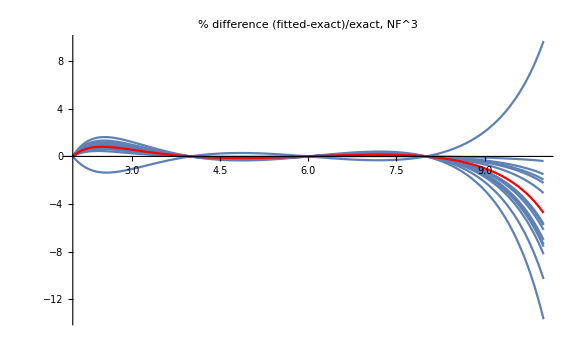

```mathematica
ggg3FittedlargeN = DoAllFits[fsmallN, flargeN, fSubLeadingLargeN, gggmoments, ggg3N0asy,ggg3N1asy, ggg3Ninf];
PlotRelativeDiffIterate[ggg3nf3  - Coefficient[ggg3N0asy + ggg3Ninf, nf ,3],ggg3FittedlargeN,3,2,10]
```

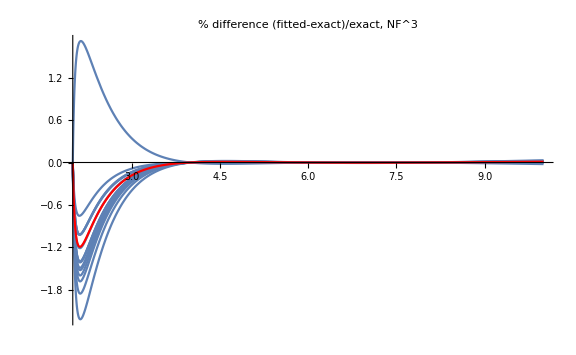

```mathematica
(* compare to total, much better accuracy *)
PlotRelativeDiffIterate[ggg3nf3 , ggg3FittedlargeN + ggg3N0asy + ggg3Ninf, 3, 2, 10]
```

#### Small-N

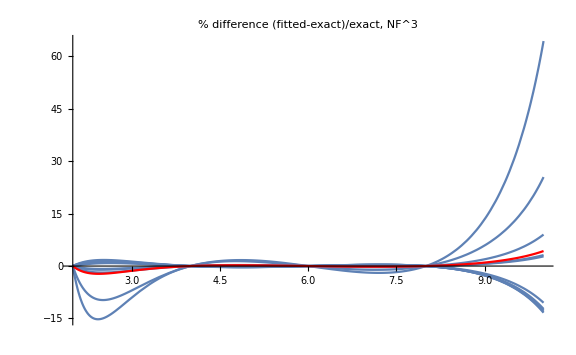

```mathematica
ggg3FittedsmallN = DoAllFits[fsmallN, flargeN, fSubLeadingSmallN, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf];
PlotRelativeDiffIterate[ggg3nf3  - Coefficient[ggg3N0asy + ggg3Ninf, nf , 3] , ggg3FittedsmallN, 3, 2, 10]
```

#### Plot Error bands

```mathematica
ggg3largeNinv = ListMellinInverse[ggg3FittedlargeN];
ggg3smallNinv = ListMellinInverse[ggg3FittedsmallN];
GraphicsRow[ShowPlots[ggg3largeNinv, ggg3smallNinv, ggg3asy, 4, defaultlegends], ImageSize -> Full]
```

-Graphics-

Remove some crazy fits, they should not matter because at later stage we will select only the smooth candidtes...

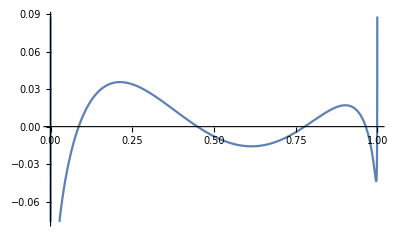

(3.20625×10^7)/(1+n)^2-314236. Lm11[n]-(203245. ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n+nf (755623./(1+n)^2+6698.7 Lm11[n]-(5876.74 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n-221883. S11m2[n])-1.04912×10^7 S11m2[n]+nf^2 (-7061.26/(1+n)^2+25.4568 Lm11[n]+(364.342 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n+981.143 S11m2[n])+nf^3 (-29.374 (1/(-1+n)-1/n)-332.988/(1+n)^2+116.259 S11m2[n]-1.50754 S13m2[n])

```mathematica
posix = 11;
PlotList[ggg3largeNinv,ggg3asy,4,1][[posix]]
ggg3FittedlargeN[[posix]]
```

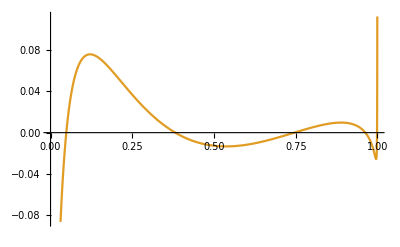

-(2.21937×10^7)/n^4+(1.96493×10^6)/n-358182. Lm11[n]-(1.83832×10^6 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n+nf (-(1.76253×10^6)/n^4+203704./n-5379.49 Lm11[n]-(162670. ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n)+nf^2 (69851.4/n^4-8682.09/n+613.888 Lm11[n]+(6922.56 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n)+nf^3 (-32.0023 (1/(-1+n)-1/n)+64.1073/n^4+9.76655/n-2.66598 S13m2[n])

```mathematica
posix = 7;
PlotList[ggg3smallNinv,ggg3asy,4,2][[posix]]
ggg3FittedsmallN[[posix]]
```

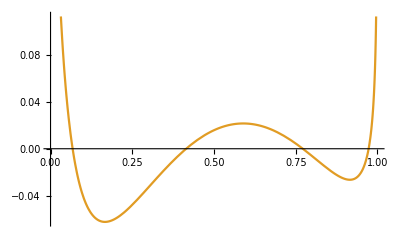

(2.14971×10^7)/n^3-(8.83725×10^6)/n^2+818433. Lm11[n]+(2.10982×10^6 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n+nf^2 (19040.6/n^3-9424.1/n^2+613.063 Lm11[n]+(1781.44 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n)+nf (53003.5/n^3+8675.41/n^2+17421.5 Lm11[n]+(11878.1 ((-1+2 n-2 n^2)/((-1+n)^2 n^2)+S[2,n]))/n)+nf^3 (-34.9375 (1/(-1+n)-1/n)+68.2383/n^3-6.15709/n^2+1.32462 S13m2[n])

```mathematica
posix = 8;
PlotList[ggg3smallNinv,ggg3asy,4,2][[posix]]
ggg3FittedsmallN[[posix]]
```

```mathematica
ggg3FittedlargeNrefined = Delete[ggg3FittedlargeN,11];
ggg3FittedsmallNrefined = Delete[ggg3FittedsmallN,8];
ggg3FittedsmallNrefined = Delete[ggg3FittedsmallNrefined,7];
ggg3largeNinvrefined = ListMellinInverse[ggg3FittedlargeNrefined];
ggg3smallNinvrefined = ListMellinInverse[ggg3FittedsmallNrefined];
GraphicsRow[ShowPlots[ggg3largeNinvrefined,ggg3smallNinvrefined,ggg3asy, 4, defaultlegends], ImageSize -> Full]
```

-Graphics-

```mathematica
{g1, g1log} = PlotErrorBand[ggg3asy, ggg3largeNinvrefined, 4,1];
{g2, g2log} = PlotErrorBand[ggg3asy, ggg3smallNinvrefined, 4,2];
GraphicsRow[{
	ShowLegends[{g1log, g2log}, Plot, defaultlegends, {1,2}],
	ShowLegends[{g1, g2}, LogLinearPlot, defaultlegends, {1,2}]
	}, ImageSize -> Full
]
```

-Graphics-

Note if you don’t include the delta function you should end up with this...

-Graphics-

```mathematica
ggg3invtotrefined = Join[ggg3largeNinvrefined, ggg3smallNinvrefined] // Flatten;
{g3, g3log} = PlotErrorBand[ggg3asy, ggg3invtotrefined, 4,3];
legend = {"small-N", "large-N", "combined"};
GraphicsRow[{
	ShowLegends[{g2log, g1log, g3log}, LogLinearPlot, legend, {1,2,3}], 
	ShowLegends[{g1, g2, g3}, Plot, legend, {1,2,3}]
	}, ImageSize -> Full
]
```

-Graphics-

#### Plot nf^3

```mathematica
ggg3asynf3 = Coefficient[ggg3asy, nf, 3];
ggg3largeNinvnf3 = Coefficient[ggg3largeNinvrefined, nf, 3];
ggg3smallNinvnf3 = Coefficient[ggg3smallNinvrefined, nf, 3];
ggg3invtotrefinednf3 = Coefficient[ggg3invtotrefined, nf, 3];
ggg3exanf3 = ReduceToHBasis[ggg3nf3x, ToKnownConstants -> True] /. hrep  /. LimitRules /. ZetaRules /. Subscript[δ, _] -> 0 // Simplify;
```

```mathematica
gtmp = ShowPlots[ggg3largeNinvnf3, ggg3smallNinvnf3, ggg3asynf3, 4, defaultlegends];
gexa3 = Plot[pifact ggg3exanf3, {x, 0, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
gexa3log = LogLinearPlot[pifact ggg3exanf3, {x, 10^-7, 1}, PlotStyle -> clist[[4]], ImageSize->Full];
GraphicsRow[{Show[{gexa3log, gtmp[[1]]}], Show[{gexa3, gtmp[[2]]}]}, ImageSize->Full]
```

-Graphics-

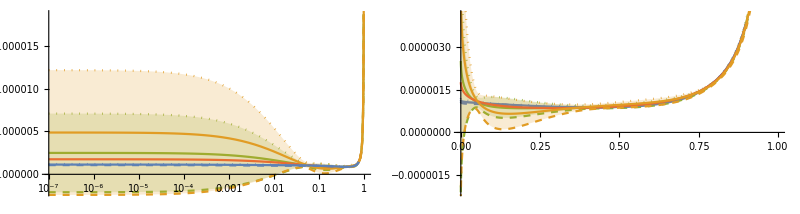

```mathematica
{g13, g13log} = PlotErrorBand[ggg3asynf3, ggg3largeNinvnf3, 4,1];
{g23, g23log} = PlotErrorBand[ggg3asynf3, ggg3smallNinvnf3, 4,2];
{g33, g33log} = PlotErrorBand[ggg3asynf3, ggg3invtotrefinednf3, 4,3];
GraphicsRow[{Show[g33log, gexa3log, g23log, g13log], Show[g33, g13, gexa3, g23]}, ImageSize -> Full]
```

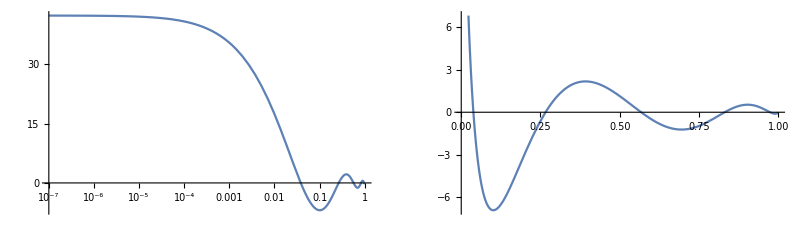

```mathematica
(* Relative difference *)
avgtotnf3 = Mean[ggg3invtotrefinednf3];
r1 = Plot[( avgtotnf3 + ggg3asynf3 - ggg3exanf3)/ggg3exanf3 * 100, {x, 0, 1} ];
r2 = LogLinearPlot[(avgtotnf3 + ggg3asynf3 - ggg3exanf3)/ggg3exanf3 * 100, {x, 10^-7, 1} ];
GraphicsRow[{r2,r1}]
```

#### Cross candidates

```mathematica
fSubLeadingtot = Join[fSubLeadingLargeN, fSubLeadingSmallN];
ggg3FittedCross = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gggmoments, ggg3N0asy,ggg3N1asy, ggg3Ninf];
(* PlotRelativeDiffSingletIterate[ggg3nf3  - Coefficient[ggg3N0asy +ggg3Ninf, nf ,3] ,gg3FittedTest,3,2,14]*)
```

```mathematica
ggg3invcross = ListMellinInverse[ggg3FittedCross];
```

```mathematica
GraphicsRow[ShowPlots[ggg3invtotrefined, ggg3invcross, ggg3asy, 4, {"combined", "cross candidates"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{g4, g4log}= PlotErrorBand[ggg3asy, ggg3invcross, 4, 5];

legend = {"small-N", "large-N", "combined", "cross candidates"};
GraphicsRow[{
	ShowLegends[{g2log, g1log, g4log, g3log}, LogLinearPlot, legend, {1,2,3,5}],
	ShowLegends[{g4, g1, g2, g3}, Plot, legend, {1,2,3,5}]
	}, ImageSize -> Full
]
```

-Graphics-

Without including the delta function in the large N limit you have something like this.

-Graphics-

#### Arch Length selection

```mathematica
thrlow = 10^-3;
thrhigh = 10^-7;
NF = 4;
```

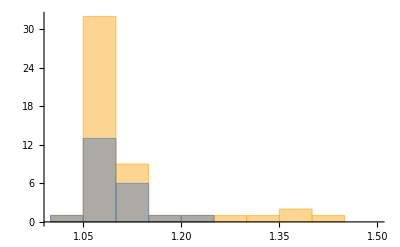

1.30137

0.76477

1.42105

1.10199

```mathematica
archdist4 = ComputeArcList[ggg3invcross,NF,thrlow,thrhigh];
archdisttot = ComputeArcList[Join[ggg3largeNinv, ggg3smallNinv] ,NF,thrlow,thrhigh];
Histogram[{archdist4, archdisttot}]

arcavg4 = Mean[archdist4]
archstd4 = StandardDeviation[archdist4]
arcavgtot = Mean[archdisttot]
arcstdtot = StandardDeviation[archdisttot]
```

```mathematica
goodcadidates = SelectSmoothCandidates[ggg3invcross, NF, thrlow, thrhigh];
good2cadidates = SelectSmoothCandidates[Join[ggg3largeNinv, ggg3smallNinv],  NF , thrlow, thrhigh];
```

Smooth candidates: 52 out of 55

Smooth candidates: 23 out of 25

```mathematica
{g5,g5log} = PlotErrorBand[ggg3asy, goodcadidates, NF, 6];
{g6,g6log} = PlotErrorBand[ggg3asy, good2cadidates, NF, 7];
legend={"cross candidate","smooth cross","combined","smooth comb"};
GraphicsRow[{
	ShowLegends[{g4log, g5log, g3log, g6log}, LogLinearPlot, legend, {5,6,3,7}], 
	ShowLegends[{g4, g5, g3, g6}, Plot, legend, {5,6,3,7}] 
	}, ImageSize -> Full
]
```

-Graphics-

```mathematica
legend = {"smooth cross", "smooth comb"};
GraphicsRow[{
  	ShowLegends[{g5log, g6log}, LogLinearPlot, legend, {6, 7}], 
  	ShowLegends[{g5, g6}, Plot, legend, {6, 7}] 
  	}, ImageSize -> Full
]
```

-Graphics-

Without including the delta function the large N limit you end up with this...

-Graphics-

#### Cherry picking

```mathematica
cherryfunctions= {1/n, 1/(n-1)};
ggg3cherry = SelectCherries[ggg3FittedCross /. S[2,n-2]/n -> S2m2,cherryfunctions];
```

Selected cherries are: 19 out of 55

```mathematica
{gcherry, gcherrylog} = PlotErrorBand[ggg3asy, ggg3cherry, 4, 4]; 
legend = {"cross candidate", "combined", "cherries"}; 
GraphicsRow[{
    	ShowLegends[{g4log, g3log, gcherrylog}, LogLinearPlot, legend, {5, 3, 4}], 
    	ShowLegends[{g4, g3, gcherry}, Plot, legend, {5, 3, 4}]
    	}, ImageSize -> Full
  ]
```

-Graphics-

```mathematica
ggg3smoothcherry = SelectSmoothCandidates[ggg3cherry, NF, thrlow, thrhigh];
Complement[ggg3cherry, ggg3smoothcherry] //MatrixForm
```

Smooth candidates: 18 out of 19

(3.80326×10^6+366374. nf-15604.6 nf^2+41.7689 nf^3-(1.83832×10^6)/x-(162670. nf)/x+(6922.56 nf^2)/x-(32.0023 nf^3)/x-358182. Log[1-x]-5379.49 nf Log[1-x]+613.888 nf^2 Log[1-x]-4.83043×10^-10 Log[x]-4.27435×10^-11 nf Log[x]+1.81899×10^-12 nf^2 Log[x]-(1.83832×10^6 Log[x])/x-(162670. nf Log[x])/x+(6922.56 nf^2 Log[x])/x-2.41521×10^-10 Log[x]^2-2.13718×10^-11 nf Log[x]^2+9.09495×10^-13 nf^2 Log[x]^2+3.69894×10^6 Log[x]^3+293756. nf Log[x]^3-11641.9 nf^2 Log[x]^3-10.6845 nf^3 Log[x]^3-1.83832×10^6 (Log[1-x] Log[x]-Log[x]^2/2+PolyLog[2,x])-162670. nf (Log[1-x] Log[x]-Log[x]^2/2+PolyLog[2,x])+6922.56 nf^2 (Log[1-x] Log[x]-Log[x]^2/2+PolyLog[2,x])-2.66598 nf^3 (-π^4/15-1/2 π^2 Log[1-x] Log[x]+Log[1-x]^3 Log[x]+3/2 Log[1-x]^2 Log[x]^2+3 Log[1-x]^2 PolyLog[2,1-x]+(π^2/2+3 Log[1-x] Log[x]-Log[x]^2/2) PolyLog[2,x]-6 Log[1-x] PolyLog[3,1-x]+3 Log[x] PolyLog[3,1-x]+2 Log[x] PolyLog[3,x]+6 PolyLog[4,1-x]-3 PolyLog[4,x]+6 PolyLog[2,2,x]-3 Log[x] Zeta[3]))

```mathematica
{gsmoothcherry, gsmoothcherrylog} = PlotErrorBand[ggg3asy, ggg3smoothcherry, 4, 2]; 
legend = {"cross candidates", "cherries", "smooth cherries"}; 
GraphicsRow[{
  	ShowLegends[{g4log, gcherrylog, gsmoothcherrylog}, LogLinearPlot, legend, {5, 4, 2}], 
  	ShowLegends[{g4, gcherry, gsmoothcherry}, Plot, legend, {5, 4, 2}]
  	}, ImageSize -> Full
 ]
```

-Graphics-

```mathematica
legend = {"smooth candidates", "smooth cherries"}; 
GraphicsRow[{
    	ShowLegends[{g5log, gsmoothcherrylog}, LogLinearPlot, legend, {6, 2}], 
    	ShowLegends[{g5, gsmoothcherry}, Plot, legend, {6, 2}]
    	}, ImageSize -> Full
  ]
```

-Graphics-

```mathematica
{gcherry3, gcherry3log} = PlotErrorBand[ggg3asynf3, Coefficient[ggg3smoothcherry,nf,3], 4, -1];
{g43, g43log} = PlotErrorBand[ggg3asynf3, Coefficient[ggg3invcross,nf,3], 4, 5];
legend = {"cross candidate","smooth cherries","analytic"};
GraphicsRow[{
	ShowLegends[{g43log, gcherry3log, gexa3log}, LogLinearPlot, legend, {5, -1, 4}], 
	ShowLegends[{g43, gcherry3, gexa3}, Plot, legend, {5, -1, 4}]
	}, ImageSize -> Full
]
```

-Graphics-

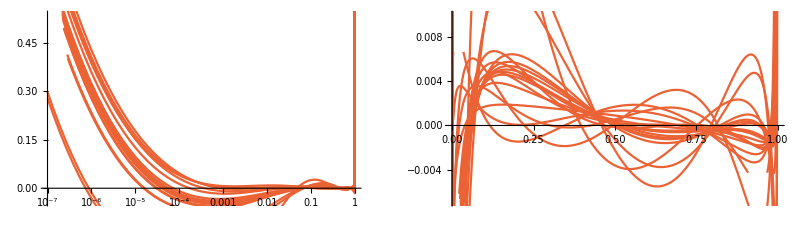

```mathematica
gcherryrep = PlotList[ggg3smoothcherry, ggg3asy, 4, 4];
glogcherryrep = LogPlotList[ggg3smoothcherry, ggg3asy, 4, 4];
GraphicsRow[{Show[glogcherryrep],Show[gcherryrep]}]
```

#### Save and final remove

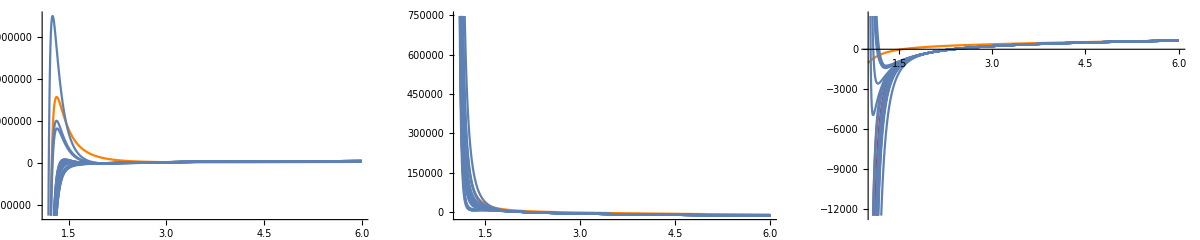

```mathematica
smoothcherryn = ggg3FittedCross[[Position[ggg3invcross, #]& /@ ggg3smoothcherry //Flatten]];
ggg3Nasy = ggg3N0asy + ggg3N1asy + ggg3Ninf;
g0 = PlotListN[ggg3Nasy, smoothcherryn, 0, -50 (4Pi)^4, 150 (4Pi)^4];
g1 = PlotListN[ggg3Nasy, smoothcherryn, 1, -40 (4Pi)^4, 30 (4Pi)^4];
g2 = PlotListN[ggg3Nasy, smoothcherryn, 2, -0.5 (4Pi)^4, 0.1 (4Pi)^4];
GraphicsRow[{
	Show[g0, PlotRange-> All],
	Show[g1, PlotRange-> All],
	Show[g2, PlotRange-> All]
}, ImageSize->Full]
```

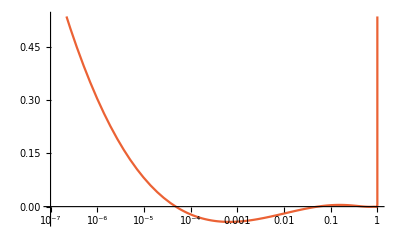
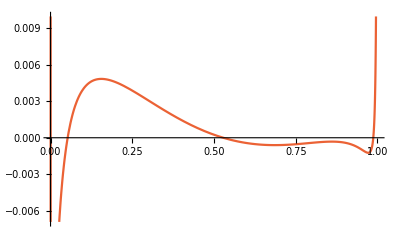
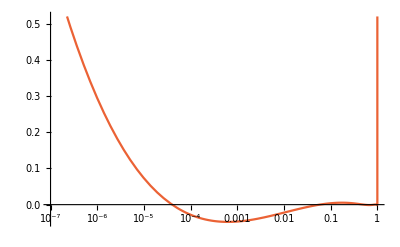
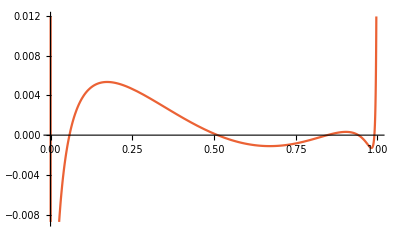
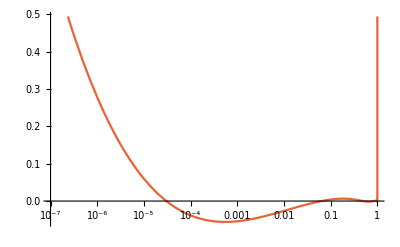
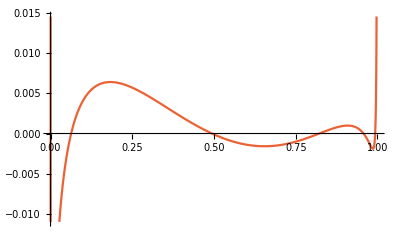
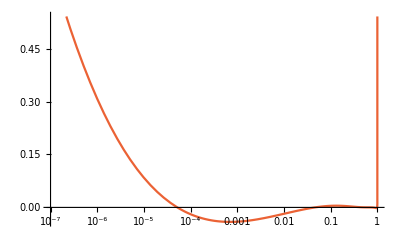
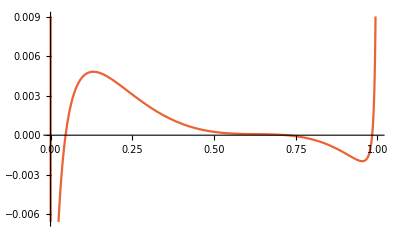
{{1,-Graphics-,-Graphics-},{2,-Graphics-,-Graphics-},{3,-Graphics-,-Graphics-},{4,-Graphics-,-Graphics-},{5,-Graphics-,-Graphics-},{6,-Graphics-,-Graphics-},{7,-Graphics-,-Graphics-},{8,-Graphics-,-Graphics-},{9,-Graphics-,-Graphics-},{10,-Graphics-,-Graphics-},{11,-Graphics-,-Graphics-},{12,-Graphics-,-Graphics-},{13,-Graphics-,-Graphics-},{14,-Graphics-,-Graphics-},{15,-Graphics-,-Graphics-},{16,-Graphics-,-Graphics-},{17,-Graphics-,-Graphics-},{18,-Graphics-,-Graphics-}}

```mathematica
MapThread[{#1, #2, #3} &, {Range[1, gcherryrep // Length], glogcherryrep, gcherryrep}]
```

```mathematica
smoothcherryn = ggg3FittedCross[[Position[ggg3invcross, #]& /@ ggg3smoothcherry //Flatten]];
exportMeList[ggg3N0asy + ggg3N1asy + ggg3Ninf, smoothcherryn, StringJoin[storepath, "ggg3nf0.c"], 0];
exportMeList[ggg3N0asy + ggg3N1asy + ggg3Ninf, smoothcherryn, StringJoin[storepath, "ggg3nf1.c"], 1];
exportMeList[ggg3N0asy + ggg3N1asy + ggg3Ninf, smoothcherryn, StringJoin[storepath, "ggg3nf2.c"], 2];
```

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg3nf0.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg3nf1.c

writing to /Users/giacomomagni/Documents/Wolfram Mathematica/Ad_N3LO/parametrised_ad/ggg3nf2.c

```mathematica
smoothcherryn //Length
```

18

#### Large N leading term variation

```mathematica
flargeN = {1,1,1,1};
fSubLeadingtot ={
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3},
	{Lm11[n],Lm11[n],Lm11[n], S13m2[n]},
	{S11m2[n],S11m2[n],S11m2[n],S11m2[n]}, 
	{Lm11m1[n],Lm11m1[n],Lm11m1[n],Lm11m1[n]},
	{1/(n-1),1/(n-1),1/(n-1),1/(n-1)}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2},
	{1/n,1/n,1/n,1/n,1/n}
};
ggg3FittedTest = DoAllFits[fsmallN, flargeN, fSubLeadingtot, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf];
```

```mathematica
invtest = ListMellinInverse[ggg3FittedTest];
invtest = SelectSmoothCandidates[invtest, 4,thrlow,thrlow];
GraphicsRow[ShowPlots[invtest, ggg3invcross, ggg3asy, 4, {"varied Large N", "cross candidates"}], ImageSize -> Full]
```

Smooth candidates: 54 out of 55

-Graphics-

#### Interpolation checks

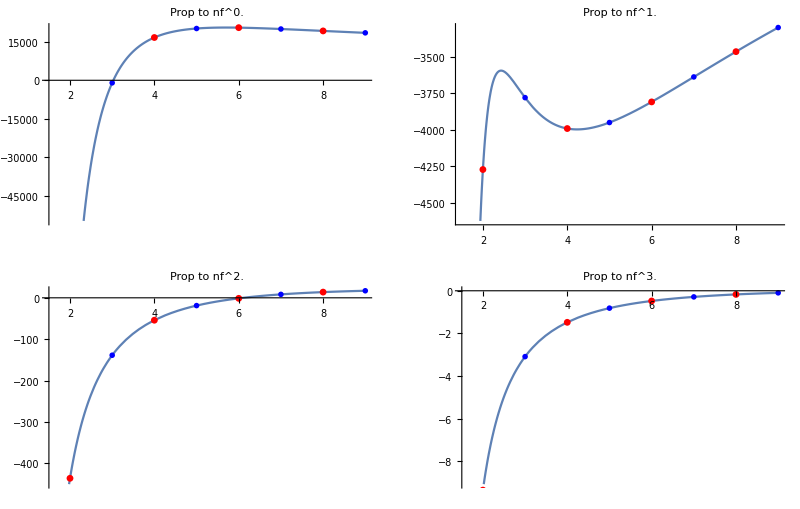

```mathematica
ggg3asytmp = ggg3N0asy + ggg3N1asy + ggg3Ninf;
GraphicsGrid[{
	{PlotInterpolation[gggmoments - ggg3asytmp, {1.5, 3,5,7,9}, 0], PlotInterpolation[gggmoments -ggg3asytmp, {1.5,3,5,7,9}, 1]},
	{PlotInterpolation[gggmoments - ggg3asytmp, {1.5, 3,5,7,9}, 2], PlotInterpolation[gggmoments -ggg3asytmp, {1.5,3,5,7,9}, 3]}
}, ImageSize->Full, PlotRange->All]
```

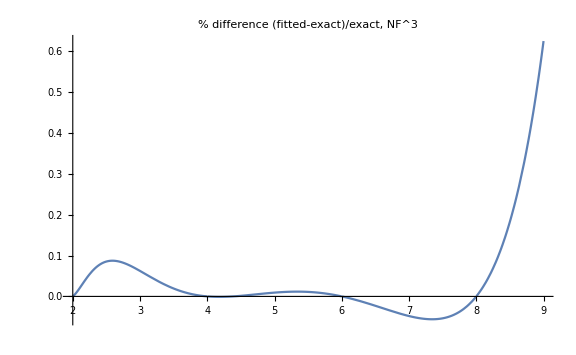

```mathematica
interpolator1 = MomentListInterpolator[gggmoments - ggg3asytmp, {2, 4, 6, 8}, 3];
PlotRelativeDiff[ggg3nf3 - Coefficient[ggg3asytmp, nf, 3], nf^3 interpolator1, 3, 2, 9]
```

#### Fixing N = 3

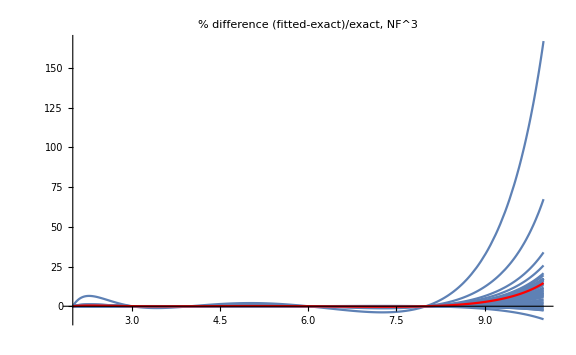

```mathematica
flargeN = {{1/n, Lm11[n]},{1/n, Lm11[n]},{1/n, Lm11[n]}, {1, Lm11[n]}};
fSubLeading = { 
	{1/(n+1),1/(n+1),1/(n+1),1/(n+1)},
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11m1[n],Lm11m1[n],Lm11m1[n], Lm11m1[n]}, 
	{S11m2[n],S11m2[n],S11m2[n], S11m2[n]}, 
	{1/(n-1),1/(n-1),1/(n-1),1/(n-1)}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2}
};

ggg3FittedInterpol3 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {3}];
PlotRelativeDiffIterate[ggg3nf3 - Coefficient[ggg3N0asy + ggg3N1asy + ggg3Ninf, nf ,3], ggg3FittedInterpol3, 3, 2, 10]
```

```mathematica
invinterpol3 = ListMellinInverse[ggg3FittedInterpol3];
invinterpol3 = SelectSmoothCandidates[invinterpol3, 4,thrlow,thrlow];
(* invinterpol = SelectCherries[ggg3FittedInterpol, 1/(n-1), 1/(n+1)]; *)
```

Smooth candidates: 43 out of 45

```mathematica
GraphicsRow[ShowPlots[invinterpol3, ggg3invcross, ggg3asy, 4, {"N=3", "cross candidates"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{gint3, gint3log} = PlotErrorBand[ggg3asy, invinterpol3, 4, 8];
legend = {"smooth candidates", "smooth cerries", "N=3"};
GraphicsRow[{
  	ShowLegends[{g5log, gsmoothcherrylog, gint3log}, LogLinearPlot, legend, {6,2,8}],
  	ShowLegends[{g5, gsmoothcherry, gint3}, Plot, legend, {6,2,8}]
  	}, ImageSize -> Full
]
```

-Graphics-

#### Fixing N = 5

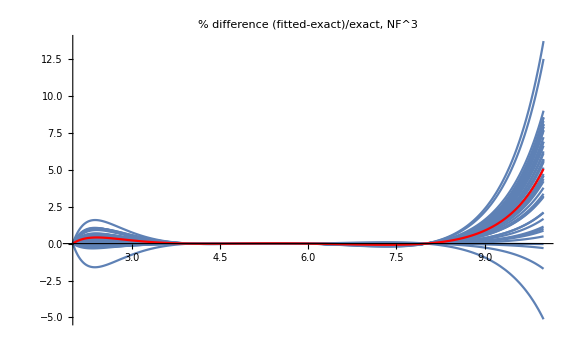

```mathematica
flargeN = {{1/n, Lm11[n]},{1/n, Lm11[n]},{1/n, Lm11[n]}, {1, Lm11[n]}};
ggg3FittedInterpol5 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {5}];
PlotRelativeDiffIterate[ggg3nf3 - Coefficient[ggg3N0asy + ggg3N1asy + ggg3Ninf, nf ,3], ggg3FittedInterpol5, 3, 2, 10]
```

```mathematica
invinterpol5 = ListMellinInverse[ggg3FittedInterpol5];
invinterpol5 = SelectSmoothCandidates[invinterpol5, 4,thrlow,thrlow];
(* invinterpol = SelectCherries[ggg3FittedInterpol, 1/(n-1), 1/(n+1)]; *)
```

Smooth candidates: 42 out of 45

```mathematica
GraphicsRow[ShowPlots[invinterpol5, ggg3invcross, ggg3asy, 4, {"N=5", "cross candidates"}], ImageSize -> Full]
```

-Graphics-

```mathematica
{gint5, gint5log} = PlotErrorBand[ggg3asy, invinterpol5, 4, -1];
```

```mathematica
legend = {"smooth candidates", "smooth cerries", "N=5"};
GraphicsRow[{
    	ShowLegends[{g5log, gsmoothcherrylog, gint5log}, LogLinearPlot, legend, {6, 2, -1}],
    	ShowLegends[{g5, gsmoothcherry, gint5}, Plot, legend, {6, 2, -1}]
    	}, ImageSize -> Full
 ]
```

-Graphics-

#### Fixing N = 7

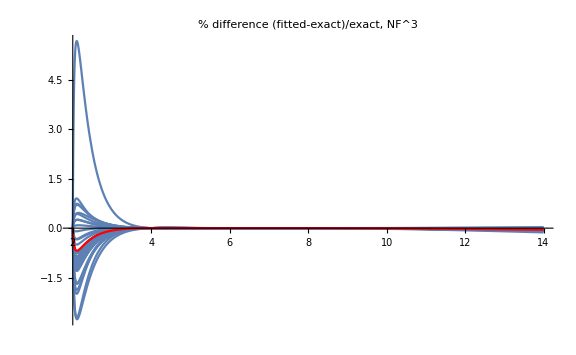

```mathematica
flargeN = {{1/n, Lm11[n]},{1/n, Lm11[n]},{1/n, Lm11[n]}, {1, Lm11[n]}};
ggg3FittedInterpol7 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {7}];
PlotRelativeDiffIterate[ggg3nf3  - Coefficient[ggg3N0asy + ggg3N1asy, nf ,3], ggg3FittedInterpol7 + ggg3Ninf, 3, 2, 14]
```

```mathematica
invinterpol7 = ListMellinInverse[ggg3FittedInterpol7];
invinterpol7 = SelectSmoothCandidates[invinterpol7, 4,thrlow,thrlow]; 
GraphicsRow[ShowPlots[invinterpol7, ggg3invcross, ggg3asy, 4, {"N=7", "cross candidate"}], ImageSize -> Full]
```

Smooth candidates: 41 out of 45

-Graphics-

```mathematica
{gint7, gint7log} = PlotErrorBand[ggg3asy, invinterpol7, 4, -2];
legend = {"smooth candidates", "N=5", "N=7"};
GraphicsRow[{
  	ShowLegends[{g5log, gint5log, gint7log}, LogLinearPlot, legend, {6,-1,-2}],
  	ShowLegends[{g5, gint5, gint7}, Plot, legend, {6,-1,-2}]
  	}, ImageSize -> Full
 ]
```

-Graphics-

#### Fixing N = 10

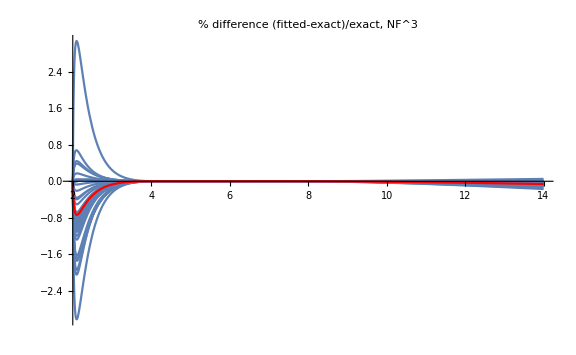

```mathematica
flargeN = {{1/n, Lm11[n]},{1/n, Lm11[n]},{1/n, Lm11[n]}, {1, Lm11[n]}};
ggg3FittedInterpol10 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {10}];
PlotRelativeDiffIterate[ggg3nf3  - Coefficient[ggg3N0asy + ggg3N1asy, nf ,3], ggg3FittedInterpol5 + ggg3Ninf, 3, 2, 14]
```

```mathematica
invinterpol10 = ListMellinInverse[ggg3FittedInterpol10];
invinterpol10 = SelectSmoothCandidates[invinterpol10, 4,thrlow,thrlow];
GraphicsRow[ShowPlots[invinterpol10, ggg3invcross, ggg3asy, 4, {"N=10", "cross candidate"}], ImageSize -> Full]
```

Smooth candidates: 40 out of 45

-Graphics-

```mathematica
{gint10, gint10log} = PlotErrorBand[ggg3asy, invinterpol10, 4, -3];
legend = {"smooth candidates", "N=5", "N=7", "N=10"};
GraphicsRow[{
  	ShowLegends[{g5log, gint5log, gint7log,gint10log}, LogLinearPlot, legend, {5,-1,-2,-3}],
  	ShowLegends[{g5, gint5, gint7, gint10}, Plot, legend, {5,-1,-2,-3}]
  	}, ImageSize -> Full
 ]
```

-Graphics-

#### Fixing 2 moments

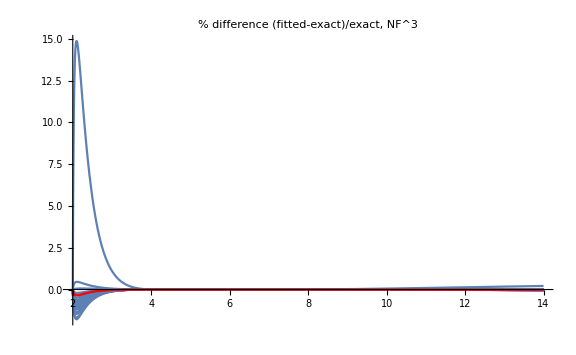

```mathematica
flargeN = {{1/n, Lm11[n], 1/(n+1)},{1/n, Lm11[n], 1/(n+1)},{1/n,Lm11[n], 1/(n+1)}, {1/n, Lm11[n], 1/(n+1)}};
fSubLeading = { 
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11m1[n],Lm11m1[n],Lm11m1[n], Lm11m1[n]}, 
	{S11m2[n],S11m2[n],S11m2[n], S11m2[n]}, 
	{1/(n-1),1/(n-1),1/(n-1),1/(n-1)}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2}
};
ggg3FittedInterpol57 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {5,7}];
PlotRelativeDiffIterate[ggg3nf3 - Coefficient[ggg3N0asy + ggg3N1asy, nf ,3], ggg3FittedInterpol57 + ggg3Ninf, 3, 2, 14]
```

```mathematica
invinterpol57 = ListMellinInverse[ggg3FittedInterpol57];
invinterpol57 = SelectSmoothCandidates[invinterpol57, 4,thrlow,thrlow];

GraphicsRow[ShowPlots[invinterpol57, ggg3invcross, ggg3asy, 4, {"N=5 and N=7", "cross candidates "}], ImageSize -> Full]
```

Smooth candidates: 35 out of 36

-Graphics-

```mathematica
{gint57, gint57log} = PlotErrorBand[ggg3asy, invinterpol3, 4, -4];
legend = {"smooth candidates", "N=5", "N=7", "N=5 and N=7"};
GraphicsRow[{
  	ShowLegends[{g5log, gint5log, gint7log, gint57log}, LogLinearPlot, legend, {6,-2,-3,-4}],
  	ShowLegends[{g5, gint5, gint7, gint57}, Plot, legend, {6,-2,-3,-4}]
  	}, ImageSize -> Full
 ]
```

-Graphics-

#### Fixing 3 moments

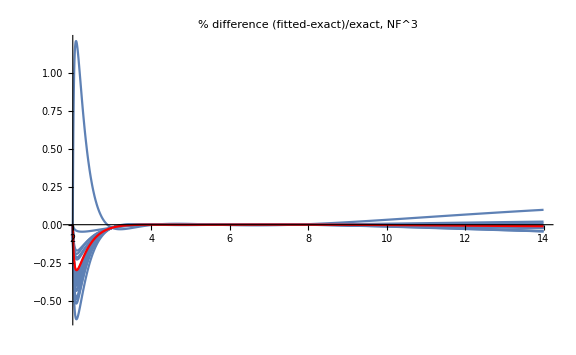

```mathematica
flargeN = {{1/n, Lm11[n], 1/(n+1), 1/(n-1)},{1/n, Lm11[n], 1/(n+1),1/(n-1)},{1/n,Lm11[n], 1/(n+1),1/(n-1)}, {1/n, Lm11[n], 1/(n+1),1/(n-1)}};
fSubLeading = { 
	{1/(n+2),1/(n+2),1/(n+2),1/(n+2)}, 
	{1/(n+1)^2,1/(n+1)^2,1/(n+1)^2,1/(n+1)^2}, 
	{1/(n+1)^3,1/(n+1)^3,1/(n+1)^3,1/(n+1)^3}, 
	{Lm11m1[n],Lm11m1[n],Lm11m1[n], Lm11m1[n]}, 
	{1/(n-1),1/(n-1),1/(n-1),1/(n-1)}, 
	{1/n^4,1/n^4,1/n^4,1/n^4},
	{1/n^3,1/n^3,1/n^3,1/n^3},
	{1/n^2,1/n^2,1/n^2,1/n^2}
};
ggg3FittedInterpol357 = InterploatedFit[fsmallN, flargeN, fSubLeading, gggmoments, ggg3N0asy, ggg3N1asy, ggg3Ninf, {3,5,7}];
PlotRelativeDiffIterate[ggg3nf3 - Coefficient[ggg3N0asy + ggg3N1asy, nf ,3], ggg3FittedInterpol357 + ggg3Ninf, 3, 2, 14]
```

```mathematica
invinterpol357 = ListMellinInverse[ggg3FittedInterpol357];
invinterpol357 = SelectSmoothCandidates[invinterpol357, 4,thrlow,thrlow];

GraphicsRow[ShowPlots[invinterpol357, ggg3invcross, ggg3asy, 4, {"N=3, N=5 and N=7", "cross candidates "}], ImageSize -> Full]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0127603}. NIntegrate obtained 4.16042 and 9.17497×10^-6 for the integral and error estimates.

Smooth candidates: 27 out of 28

-Graphics-

```mathematica
{gint357, gint357log} = PlotErrorBand[ggg3asy, invinterpol357, 4, -5];
legend = {"smooth candidates", "N=3", "N=5 and N=7", "N=3, N=5 and N=7"};
GraphicsRow[{
  	ShowLegends[{g5log, gint3log, gint57log, gint357log}, LogLinearPlot, legend, {6,8,-4,-5}],
  	ShowLegends[{g5, gint3,gint57, gint357}, Plot, legend, {6,8,-4,-5}]
  	}, ImageSize -> Full
 ]
```

-Graphics-